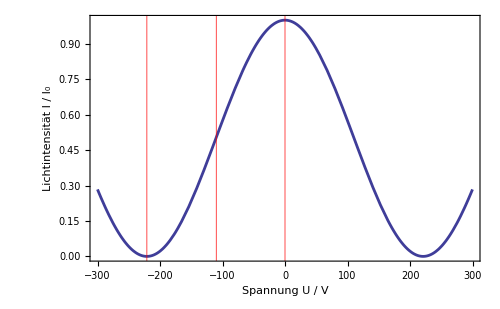

```mathematica
Ι=Cos[π U/(2*221)]^2;
p1=Plot[Ι,{U,-300,300},
ImageSize->500,
PlotStyle->AbsoluteThickness[2],
Frame->True,
FrameStyle->Thickness[0.004],
LabelStyle->Directive[FontSize->14],
FrameLabel->{"Spannung U / V","Lichtintensität I / I_0"},
GridLines->{{0,-110,-221},{}},
GridLinesStyle->Red,
Axes->False]
```

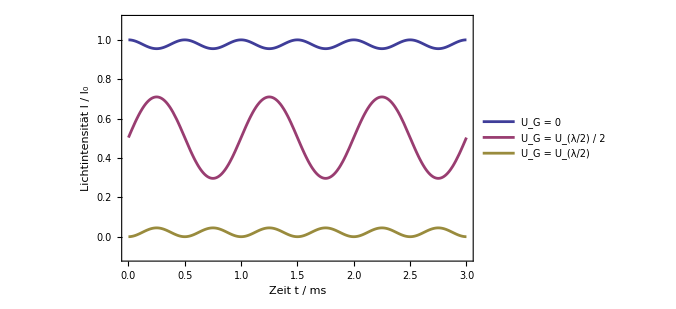

```mathematica
l1={U->U0+A Sin[2π*1000*t/1000]};
l2a={U0->0,A->30};
l2b={U0->-110,A->30};
l2c={U0->-221,A->30};
p2=Plot[{Ι/.l1/.l2a,Ι/.l1/.l2b,Ι/.l1/.l2c},{t,0,3},
PlotRange->{-0.1,1.1},
PlotStyle->AbsoluteThickness[2],
FrameStyle->Thickness[0.004],
ImageSize->500,
Frame->True,
FrameLabel->{"Zeit t / ms","Lichtintensität I / I_0"},
LabelStyle->Directive[FontSize->14],
(*PlotLegends->Style[Placed[{"U_G = 0","U_G = U_(λ/2) / 2","U_G = U_(λ/2)"},14,{0.78,0.27}]]*)
PlotLegends->Placed[{"U_G = 0","U_G = U_(λ/2) / 2","U_G = U_(λ/2)"},{0.78,0.27}]
]
```

```mathematica
p3=Plot3D[Sin[π(U0+A Sin[2 π *t])/(2*221)]^2/.A->30,{U0,-300,300},{t,0,3},ImageSize->400,AxesLabel->{"U_G / V","Zeit t / ms","Lichtintensität \n I / I_0"},MeshFunctions->{#1&,#1&},Mesh->{{-221,-110,0},50},MeshStyle->{{Red,Thickness[0.01]},Black} ,LabelStyle->Directive[FontSize->12]]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"..\\img\\Pocktheo1.pdf",p1]
Export[NotebookDirectory[]<>"..\\img\\Pocktheo2.pdf",p2]
```

C:\fpgithub\0924-FarPock\stuff\..\img\Pocktheo1.pdf

C:\fpgithub\0924-FarPock\stuff\..\img\Pocktheo2.pdf

```mathematica
image=Rasterize[p3,"Image",ImageResolution->200]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"..\\img\\Pocktheo3.pdf",image]
```

C:\fpgithub\0924-FarPock\stuff\..\img\Pocktheo3.pdf